```mathematica
Clear["Global`*"];
adagfxn[n_,m_] := N[Sqrt[m]] /; m-n == 1;
adagfxn[n_,m_] := 0. /; m-n ≠ 1;
adag[basissize_] := Table[adagfxn[n,m],{n,0,basissize-1},{m,0,basissize-1}];
a[basissize_] := ConjugateTranspose[adag[basissize]];
x[basissize_] := Sqrt[1 / 2.](a[basissize] + adag[basissize]);
p[basissize_] := -I Sqrt[2.] (a[basissize] -  adag[basissize]);
h0[basissize_] := DiagonalMatrix[Table[n + 1 / 2,{n, 0, basissize - 1}]] ;
H[basissize_,g_]:= h0[basissize] + g x[basissize].x[basissize].x[basissize].x[basissize]/4;
S[basissize_] := Transpose[Normalize /@ Eigenvectors[x[basissize]]];
fn[basissize_,g_,n_] := Sort[Eigenvalues[N[H[basissize,g]]]][[n]];
toposbasis[basissize_,evec_]:= ConjugateTranspose[S[basissize]].evec;
xvals[basissize_]:= Table[(ConjugateTranspose[S[basissize]].x[basissize].S[basissize])[[m]][[m]],{m,basissize}];
```

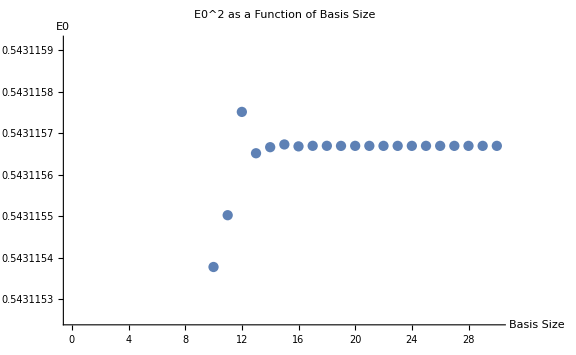

```mathematica
n = 0; g=.275;
ListPlot[Table[{basissize,fn[basissize,g,n+1]},{basissize,5,30}],PlotLabel->"E0^2 as a Function of Basis Size",AxesLabel->{"Basis Size","E0"},ImageSize->Large]
```

0.543116

{-0.998536,0,0.053436,0,0.00761647,0,-0.00339876,0,0.000477391,0,0.0000817578,0,-0.0000670487,0,0.0000197123,0}

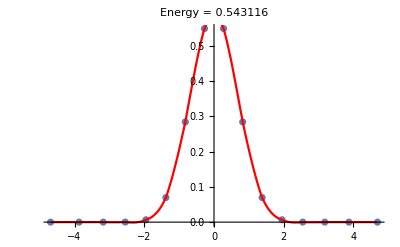

```mathematica
n = 0; bs = 16; g=.275;
{evals,evecs} = Eigensystem[N[H[bs,g]]];
{evals,evecs} = Transpose@SortBy[Transpose[{evals,evecs}],First];
e0 = Chop[evals[[n+1]]]
e0wf = Chop[evecs[[n+1]]]
energy[e0_,x_] := e0 /; e0 ≥ V[x];
h0eigenfxn[n_,x_] := N[(2^n Factorial[n] Sqrt[Pi])^(-1 / 2) Exp[-x^2 / 2] HermiteH[n,x]];
fun = Interpolation[Transpose[{xvals[bs],Abs[toposbasis[bs,e0wf]]^2}]];
norm2 = NIntegrate[fun[x],{x,-4.68,4.68}];
p2 = ListPlot[Transpose[{xvals[bs],Abs[toposbasis[bs,e0wf]]^2/norm2}],PlotRange->All];
p3 = Plot[fun[x]/norm2,{x,-4.68,4.68},PlotStyle->Hue[1],PlotRange->All];
Show[p2,p3,PlotLabel-> StringForm["Energy = ``",e0]]
```

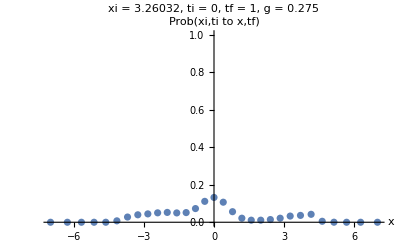

```mathematica
Kmat[basissize_,g_,T_, t_]:= ConjugateTranspose[S[basissize]].MatrixExp[-I H [basissize,g](T-t)].S[basissize];
probabilities[basissize_,g_,T_, t_]:= Abs[Kmat[basissize,g,T, t]]^2;
bas = 31; T = 1; t = 0; xx = 15; g = 0.275;
ListPlot[Transpose[{xvals[bas],probabilities[bas,g,T,t][[xx]]}],PlotLabel-> StringForm["xi = ``, ti = ``, tf = ``, g = ``",xvals[bas][[xx]],t,T,g],AxesLabel->{"x","Prob(xi,ti to x,tf)"},PlotRange-> {{-4,4}{0,0.25}}]
animation = Table[ListPlot[Transpose[{xvals[bas],probabilities[bas,g,TF/10,t][[xx]]}],PlotLabel-> StringForm["xi = ``, ti = ``, tf = ``, g = ``",xvals[bas][[xx]],t,N[TF/10],g],AxesLabel->{"x","Prob(xi,ti to x,tf)"},PlotRange-> {{-4,4},{0,1}}],{TF,0,100}];
ListAnimate[animation]
```

```mathematica
DSolve[{y''[x] + y[x] + 2 (y[x])^3 == 0},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→-1/(√2)ⅈ √(1+√(1+4 C[1])) JacobiSN[1/(√2)(√(x^2-x^2 √(1+4 C[1])+2 x C[2]-2 x √(1+4 C[1]) C[2]+C[2]^2-√(1+4 C[1]) C[2]^2)),(1+√(1+4 C[1]))/(1-√(1+4 C[1]))]},{y[x]→1/(√2)ⅈ √(1+√(1+4 C[1])) JacobiSN[1/(√2)(√(x^2-x^2 √(1+4 C[1])+2 x C[2]-2 x √(1+4 C[1]) C[2]+C[2]^2-√(1+4 C[1]) C[2]^2)),(1+√(1+4 C[1]))/(1-√(1+4 C[1]))]}}

9.21031/(√x)

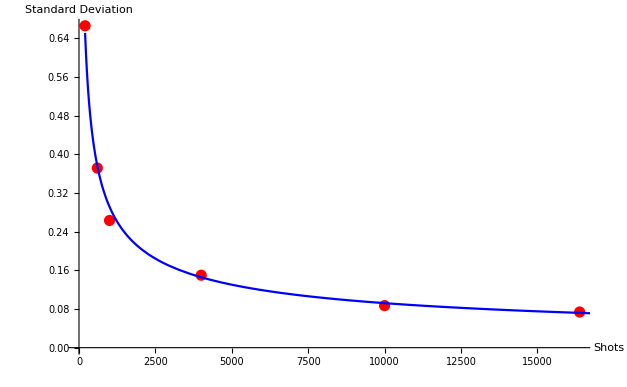

```mathematica
data = {{200,.66590624},{600,.3716589},{1000,.2631620},{4000,.1498938},{16384,.0738},{10000,.0870}};
fxn = Fit[data,{1/Sqrt[x]},x]
Show[ListPlot[data,PlotStyle->Red],Plot[9.21031/Sqrt[x],{x,200,17000},PlotRange->All,PlotStyle->Blue],AxesLabel->{"Shots","Standard Deviation"}]
```

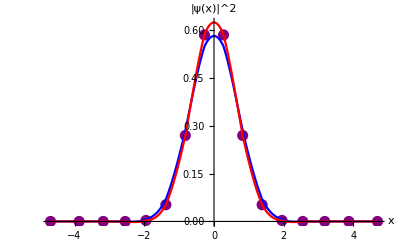

0.55076

```mathematica
n = 0; bs = 16; g=.275;
e0wfvqe = {0.9941625159144055,0,-0.10789296525139842,0,0,0,0,0,0,0,0,0,0,0,0,0};
h0eigenfxn[n_,x_] := N[(2^n Factorial[n] Sqrt[Pi])^(-1 / 2) Exp[-x^2 / 2] HermiteH[n,x]];
funvqe = Interpolation[Transpose[{xvals[bs],Abs[toposbasis[bs,e0wfvqe]]^2}]];
norm2vqe= NIntegrate[funvqe[x],{x,-4.68,4.68}];
p2 = ListPlot[Transpose[{xvals[bs],Abs[toposbasis[bs,e0wfvqe]]^2/norm2vqe}],PlotRange->All,PlotStyle->{Purple,AbsolutePointSize[8]}];
p3 = Plot[funvqe[x]/norm2vqe,{x,-4.68,4.68},PlotStyle->Hue[1]];
p5 = Plot[fun[x]/norm2,{x,-4.68,4.68},PlotStyle->Blue,PlotRange->All];
plot = Show[p2,p5,p3,PlotRange->All,AxesLabel->{"x","|ψ(x)|^2"}];
ShowLegend[plot,{{{Graphics[{Purple, Disk[{0,0},.05]}],"Discrete VQE"},{Graphics[{Thickness[.1],Red,Line[{{0,0},{2,0}}]}],"VQE Interpolation"},{Graphics[{Thickness[.1],Blue,Line[{{0,0},{2,0}}]}],"Matrix Interpolation"}},LegendPosition->{0.1,0.1},LegendSize->{0.6,0.4},LegendShadow->False}]
Conjugate[e0wfvqe].H[bs,g].e0wfvqe
```

```mathematica
Clear["Global`*"];
adagfxn[n_,m_] := N[Sqrt[m]] /; m-n == 1;
adagfxn[n_,m_] := 0. /; m-n ≠ 1;
adag[basissize_] := Table[adagfxn[n,m],{n,0,basissize-1},{m,0,basissize-1}];
a[basissize_] := ConjugateTranspose[adag[basissize]];
x[basissize_] := Sqrt[1 / 2.](a[basissize] + adag[basissize]);
p[basissize_] := -I Sqrt[2.] (a[basissize] -  adag[basissize]);
h0[basissize_] := DiagonalMatrix[Table[n + 1 / 2,{n, 0, basissize - 1}]] ;
G[basissize_,g_]:= h0[basissize] + g x[basissize].x[basissize].x[basissize].x[basissize]/4;
H[basissize_,g_]:=  -KroneckerProduct[G[basissize,g],IdentityMatrix[basissize]] + KroneckerProduct[IdentityMatrix[basissize],G[basissize,g]];
S[basissize_] := KroneckerProduct[Transpose[Normalize /@ Eigenvectors[x[basissize]]],Transpose[Normalize /@ Eigenvectors[x[basissize]]]];
fn[basissize_,g_,n_] := Sort[Eigenvalues[N[H[basissize,g]]]][[n]];
toposbasis[basissize_,evec_]:= ConjugateTranspose[S[basissize]].evec;
xvals[basissize_]:= Table[(ConjugateTranspose[S[basissize]].x[basissize].S[basissize])[[m]][[m]],{m,basissize}];
```

```mathematica
g = .275; bs = 16;
Transpose@SortBy[Transpose[Chop[Eigensystem[H[bs,g].H[bs,g]]]],First]
```

```mathematica
Clear["Global`*"];
adagfxn[n_,m_] := N[Sqrt[m]] /; m-n == 1;
adagfxn[n_,m_] := 0. /; m-n ≠ 1;
adag[basissize_] := Table[adagfxn[n,m],{n,0,basissize-1},{m,0,basissize-1}];
a[basissize_] := ConjugateTranspose[adag[basissize]];
x[basissize_] := Sqrt[1 / 2.](a[basissize] + adag[basissize]);
p[basissize_] := -I Sqrt[2.] (a[basissize] -  adag[basissize]);
h0[basissize_] := DiagonalMatrix[Table[n + 1 / 2,{n, 0, basissize - 1}]] ;
G[basissize_,g_]:= p[basissize].p[basissize]/4 + x[basissize].x[basissize] + g x[basissize].x[basissize].x[basissize].x[basissize]/4;
H[basissize_,g_]:=  -KroneckerProduct[G[basissize,g],IdentityMatrix[basissize]] + KroneckerProduct[IdentityMatrix[basissize],G[basissize,g]];
S[basissize_] := KroneckerProduct[Transpose[Normalize /@ Eigenvectors[x[basissize]]],Transpose[Normalize /@ Eigenvectors[x[basissize]]]];
fn[basissize_,g_,n_] := Sort[Eigenvalues[N[H[basissize,g]]]][[n]];
toposbasis[basissize_,evec_]:= ConjugateTranspose[S[basissize]].evec;
xvals[basissize_]:= Table[(ConjugateTranspose[S[basissize]].x[basissize].S[basissize])[[m]][[m]],{m,basissize}];
```

```mathematica
Clear["Global`*"];
actual = {-0.998536323226009,0,0.05343603301244659,0,0.007616466296343005,0,-0.003398756394736359,0,0.00047739067576524303,0,0.0000817577918072459,0,-0.00006704873471568644,0,0.00001971229985285389,0};
bas = Length[actual];
res = Flatten[KroneckerProduct[actual,actual]];
evec = Table[a[i],{i,bas}];
tensored = Flatten[KroneckerProduct[evec,evec]];
tensored // MatrixForm;
answer = NSolve[Table[res[[k]]==tensored[[k]],{k,bas}],evec];
evec/.answer[[1]]
```

{-0.998536,0.,0.053436,0.,0.00761647,0.,-0.00339876,0.,0.000477391,0.,0.0000817578,0.,-0.0000670487,0.,0.0000197123,0.}

```mathematica
(H[16,0.275].{-0.998536323226009,0.,0.05343603301244659,0.,0.007616466296343005,0.,-0.003398756394736359,0.,0.00047739067576524303,0.,0.0000817577918072459,0.,-0.00006704873471568644,0.,0.00001971229985285389,0.})/({-0.998536323226009,0.,0.05343603301244659,0.,0.007616466296343005,0.,-0.003398756394736359,0.,0.00047739067576524303,0.,0.0000817577918072459,0.,-0.00006704873471568644,0.,0.00001971229985285389,0.}+0.00000000000000000000001)
```

{0.543116,0.,0.543116,0.,0.543116,0.,0.543116,0.,0.543116,0.,0.543116,0.,0.543116,0.,0.543116,0.}